```mathematica
getstdx[V1_, V2_,x1startest_, x1endest_,precision_]:=Module[{x1,x2,x3,x1start, x1end,x1new,area},
x1start=x1startest;
x1end=x1endest;
While[x1end-x1start>precision,
x1new = (x1start+x1end)/2;
x2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,x1new,a}]==V1,{a,x1new/2}];
area=NIntegrate[ⅇ^(x^2),{x,x2,-(x1new+x2)}];
If[area>V2,x1start=x1new,x1end=x1new]
];
x1=(x1start+x1end)/2;
x2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,x1,a}]==V1,{a,x1/2}];
x3=-(x1+x2);
Return[{x1, x2, x3}]
];

density[val_, ϵ_]:=If[Abs[val]<ϵ,Return[ⅇ^(val^2)],Return[ⅇ^(ϵ(2Abs[val]-ϵ))]];

pdiff[V1_,V2_,ϵ_,precision_]:=
Module[{x1,x2,x3,y1,y2,diff,x1start,x1end,x1new,area,smoothvol,values},
(*Volume of the smooth region*)
smoothvol = Integrate[ⅇ^(x^2),{x, -ϵ, ϵ}];

(*Computes the position of the isoperimetric triple interval*)
If[V1+V2≤smoothvol,
y1 =a/.FindRoot[Integrate[ⅇ^(x^2),{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,y1,a}]==V2/2,{a,y1}];,
If[V1≤smoothvol,
y1 =a/.FindRoot[Integrate[ⅇ^(x^2),{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V2+V1-smoothvol)/2,{a,ϵ}];,

y1 =a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V1-smoothvol)/2,{a,ϵ}];
y2=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,y1,a}]==V2/2,{a,y1}];
];
];

(*Computes the position of the isoperimetric double interval*)
If[V1≥smoothvol/2,
x1 =-a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V1-smoothvol)/2,{a,ϵ}];
x2=-a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V2-smoothvol)/2,{a,-x1}];
x3=-(x1+x2);,
If[V2≤ smoothvol/2,
values=getstdx[V1, V2, -y2, -y1,precision];
x1=values[[1]];
x2=values[[2]];
x3=values[[3]];,

x1=a/.FindRoot[Integrate[ⅇ^(x^2), {x, a, -ϵ-a}]==V1,{a, 0}];
x2=-ϵ-x1;
x3=a/.FindRoot[Integrate[ⅇ^(x^2), {x, x2, ϵ}]+Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==V2,{a,ϵ}];
If[x3<ϵ,values=getstdx[V1, V2, -y2, -y1,precision];
x1=values[[1]];
x2=values[[2]];
x3=values[[3]];];
];
];
Print["x1=",x1," x2=", x2," x3=", x3,"y1=",y1," y2=",y2];
diff=2 density[y1,ϵ]+2 density[y2,ϵ]-density[x1,ϵ]-density[x2,ϵ]-density[x3,ϵ];
Return[diff];
]
```

```mathematica
table[range_,blocks_,precision_,ϵ_]:=
Module[{g},
g=Table[0,{i,blocks},{j,blocks}];
For[i=1,i≤blocks,i++,
For[j=i,j≤blocks,j++,
g[[i,j]]=pdiff[i*range/blocks,j*range/blocks,ϵ,precision];
]
];
Return[g];
]
```

```mathematica
tabletest[range_,blocks_,precision_,ϵ_]:=
Module[{g},
g=ParallelTable[pdiff[i*10/5,j*range/blocks,ϵ,precision],{i,10},{j,i,blocks}];
Return[g];
]
```

```mathematica
g=tabletest[1000, 20, 0.000001,4]//PadLeft
```

x1=-1.69878 x2=-0.600814 x3=2.29959y1=1.36436 y2=2.15223

x1=-2.11595 x2=-0.502206 x3=2.61816y1=1.90164 y2=2.49301

x1=-1.71199 x2=-0.753364 x3=2.46536y1=1.36436 y2=2.31744

x1=-2.11664 x2=-0.548006 x3=2.66464y1=1.90164 y2=2.5376

x1=-1.72014 x2=-0.835633 x3=2.55577y1=1.36436 y2=2.41022

x1=-2.11721 x2=-0.584676 x3=2.70188y1=1.90164 y2=2.57395

x1=-1.72617 x2=-0.891308 x3=2.61748y1=1.36436 y2=2.47416

x1=-2.1177 x2=-0.615173 x3=2.73287y1=1.90164 y2=2.60456

x1=-1.731 x2=-0.933066 x3=2.66407y1=1.36436 y2=2.52267

x1=-2.11814 x2=-0.641227 x3=2.75936y1=1.90164 y2=2.63095

x1=-2.11853 x2=-0.663949 x3=2.78248y1=1.90164 y2=2.65412

x1=-1.73507 x2=-0.96631 x3=2.70138y1=1.36436 y2=2.56163

x1=-2.11888 x2=-0.684062 x3=2.80295y1=1.90164 y2=2.67476

x1=-1.73859 x2=-0.993834 x3=2.73243y1=1.36436 y2=2.59409

x1=-2.11921 x2=-0.702089 x3=2.8213y1=1.90164 y2=2.69334

x1=-1.74171 x2=-1.01726 x3=2.75897y1=1.36436 y2=2.62186

x1=-2.11951 x2=-0.718459 x3=2.83797y1=1.90164 y2=2.71022

x1=-1.74451 x2=-1.03761 x3=2.78212y1=1.36436 y2=2.6461

x1=-2.1198 x2=-0.733376 x3=2.85317y1=1.90164 y2=2.7257

x1=-1.74706 x2=-1.05556 x3=2.80262y1=1.36436 y2=2.66759

x1=-2.12006 x2=-0.747086 x3=2.86715y1=1.90164 y2=2.73996

x1=-1.7494 x2=-1.07162 x3=2.82102y1=1.36436 y2=2.68686

x1=-2.12031 x2=-0.759805 x3=2.88012y1=1.90164 y2=2.7532

x1=-1.75157 x2=-1.08611 x3=2.83768y1=1.36436 y2=2.70432

x1=-2.12055 x2=-0.771614 x3=2.89216y1=1.90164 y2=2.76553

x1=-1.75359 x2=-1.09932 x3=2.85291y1=1.36436 y2=2.72027

x1=-2.12077 x2=-0.782649 x3=2.90342y1=1.90164 y2=2.77708

x1=-1.75548 x2=-1.11143 x3=2.86691y1=1.36436 y2=2.73495

x1=-2.12099 x2=-0.793026 x3=2.91401y1=1.90164 y2=2.78793

x1=-1.75726 x2=-1.12261 x3=2.87988y1=1.36436 y2=2.74854

x1=-2.12119 x2=-0.802768 x3=2.92396y1=1.90164 y2=2.79816

x1=-1.75895 x2=-1.133 x3=2.89194y1=1.36436 y2=2.76119

x1=-2.12139 x2=-0.811974 x3=2.93336y1=1.90164 y2=2.80783

x1=-1.76055 x2=-1.14268 x3=2.90322y1=1.36436 y2=2.773

x1=-2.17564 x2=-0.489049 x3=2.66469y1=1.97188 y2=2.54234

x1=-1.76206 x2=-1.15175 x3=2.91381y1=1.36436 y2=2.78409

x1=-2.17606 x2=-0.525835 x3=2.7019y1=1.97188 y2=2.57789

x1=-1.76351 x2=-1.16027 x3=2.92378y1=1.36436 y2=2.79454

x1=-2.17642 x2=-0.556466 x3=2.73289y1=1.97188 y2=2.60792

x1=-1.7649 x2=-1.1683 x3=2.9332y1=1.36436 y2=2.80441

x1=-2.17674 x2=-0.582662 x3=2.7594y1=1.97188 y2=2.63389

x1=-1.91752 x2=-0.548556 x3=2.46608y1=1.65807 y2=2.33096

x1=-2.17702 x2=-0.605484 x3=2.78251y1=1.97188 y2=2.65672

x1=-1.92064 x2=-0.635649 x3=2.55628y1=1.65807 y2=2.41903

x1=-2.17728 x2=-0.62571 x3=2.80299y1=1.97188 y2=2.67709

x1=-1.92293 x2=-0.694923 x3=2.61786y1=1.65807 y2=2.48064

x1=-2.17752 x2=-0.64382 x3=2.82134y1=1.97188 y2=2.69545

x1=-1.92478 x2=-0.73962 x3=2.6644y1=1.65807 y2=2.52778

x1=-2.17774 x2=-0.660233 x3=2.83797y1=1.97188 y2=2.71215

x1=-1.92634 x2=-0.775321 x3=2.70166y1=1.65807 y2=2.56582

x1=-2.17794 x2=-0.675224 x3=2.85317y1=1.97188 y2=2.72747

x1=-1.92769 x2=-0.804995 x3=2.73268y1=1.65807 y2=2.59764

x1=-2.17813 x2=-0.689022 x3=2.86716y1=1.97188 y2=2.7416

x1=-1.92889 x2=-0.830296 x3=2.75918y1=1.65807 y2=2.62494

x1=-2.17831 x2=-0.701796 x3=2.88011y1=1.97188 y2=2.75472

x1=-1.92997 x2=-0.852356 x3=2.78232y1=1.65807 y2=2.64882

x1=-2.17848 x2=-0.713724 x3=2.89221y1=1.97188 y2=2.76696

x1=-2.17865 x2=-0.724807 x3=2.90345y1=1.97188 y2=2.77841

x1=-1.93095 x2=-0.871846 x3=2.8028y1=1.65807 y2=2.67001

x1=-2.1788 x2=-0.735241 x3=2.91404y1=1.97188 y2=2.78918

x1=-1.93187 x2=-0.889325 x3=2.82119y1=1.65807 y2=2.68904

x1=-2.17895 x2=-0.745024 x3=2.92397y1=1.97188 y2=2.79935

x1=-1.93271 x2=-0.905125 x3=2.83783y1=1.65807 y2=2.70631

x1=-2.17909 x2=-0.754303 x3=2.93339y1=1.97188 y2=2.80896

x1=-1.9335 x2=-0.919551 x3=2.85305y1=1.65807 y2=2.7221

x1=-2.22303 x2=-0.478936 x3=2.70196y1=2.02684 y2=2.58175

x1=-1.93424 x2=-0.932809 x3=2.86705y1=1.65807 y2=2.73664

x1=-2.22331 x2=-0.509615 x3=2.73292y1=2.02684 y2=2.61123

x1=-1.93494 x2=-0.945064 x3=2.88001y1=1.65807 y2=2.75011

x1=-2.22355 x2=-0.535883 x3=2.75944y1=2.02684 y2=2.63678

x1=-1.93561 x2=-0.956463 x3=2.89207y1=1.65807 y2=2.76265

x1=-2.22377 x2=-0.558749 x3=2.78252y1=2.02684 y2=2.65929

x1=-1.93624 x2=-0.967102 x3=2.90334y1=1.65807 y2=2.77437

x1=-2.22397 x2=-0.57905 x3=2.80302y1=2.02684 y2=2.67939

x1=-1.93684 x2=-0.977078 x3=2.91392y1=1.65807 y2=2.78538

x1=-2.22416 x2=-0.597201 x3=2.82136y1=2.02684 y2=2.69753

x1=-1.93742 x2=-0.986467 x3=2.92389y1=1.65807 y2=2.79575

x1=-2.22433 x2=-0.613674 x3=2.838y1=2.02684 y2=2.71406

x1=-1.93798 x2=-0.995327 x3=2.9333y1=1.65807 y2=2.80556

x1=-2.22448 x2=-0.628751 x3=2.85323y1=2.02684 y2=2.72922

x1=-2.03606 x2=-0.520462 x3=2.55652y1=1.80564 y2=2.42748

x1=-2.22463 x2=-0.6426 x3=2.86723y1=2.02684 y2=2.74323

x1=-2.03735 x2=-0.580696 x3=2.61805y1=1.80564 y2=2.48692

x1=-2.22477 x2=-0.655357 x3=2.88012y1=2.02684 y2=2.75623

x1=-2.03838 x2=-0.626154 x3=2.66453y1=1.80564 y2=2.53275

x1=-2.2249 x2=-0.66732 x3=2.89222y1=2.02684 y2=2.76837

x1=-2.03924 x2=-0.662537 x3=2.70178y1=1.80564 y2=2.56993

x1=-2.22502 x2=-0.67847 x3=2.90349y1=2.02684 y2=2.77974

x1=-2.03999 x2=-0.692786 x3=2.73278y1=1.80564 y2=2.60113

x1=-2.22514 x2=-0.688903 x3=2.91404y1=2.02684 y2=2.79044

x1=-2.04065 x2=-0.718638 x3=2.75929y1=1.80564 y2=2.62797

x1=-2.22525 x2=-0.698773 x3=2.92403y1=2.02684 y2=2.80053

x1=-2.04125 x2=-0.74115 x3=2.7824y1=1.80564 y2=2.65149

x1=-2.22536 x2=-0.708022 x3=2.93338y1=2.02684 y2=2.81008

x1=-2.04179 x2=-0.761111 x3=2.8029y1=1.80564 y2=2.6724

x1=-2.26217 x2=-0.470788 x3=2.73296y1=2.07177 y2=2.61448

x1=-2.04229 x2=-0.77898 x3=2.82127y1=1.80564 y2=2.6912

x1=-2.26237 x2=-0.497047 x3=2.75941y1=2.07177 y2=2.63962

x1=-2.04275 x2=-0.795168 x3=2.83792y1=1.80564 y2=2.70828

x1=-2.26255 x2=-0.519972 x3=2.78252y1=2.07177 y2=2.66181

x1=-2.04319 x2=-0.809933 x3=2.85312y1=1.80564 y2=2.72391

x1=-2.26271 x2=-0.540284 x3=2.80299y1=2.07177 y2=2.68166

x1=-2.04359 x2=-0.823531 x3=2.86712y1=1.80564 y2=2.73831

x1=-2.26285 x2=-0.558562 x3=2.82142y1=2.07177 y2=2.69959

x1=-2.04398 x2=-0.836082 x3=2.88006y1=1.80564 y2=2.75166

x1=-2.26299 x2=-0.575021 x3=2.83801y1=2.07177 y2=2.71594

x1=-2.04434 x2=-0.847784 x3=2.89213y1=1.80564 y2=2.76409

x1=-2.26312 x2=-0.590142 x3=2.85326y1=2.07177 y2=2.73096

x1=-2.04469 x2=-0.85871 x3=2.9034y1=1.80564 y2=2.77573

x1=-2.26323 x2=-0.603985 x3=2.86722y1=2.07177 y2=2.74484

x1=-2.04502 x2=-0.868947 x3=2.91396y1=1.80564 y2=2.78666

x1=-2.26335 x2=-0.61685 x3=2.8802y1=2.07177 y2=2.75773

x1=-2.04533 x2=-0.878616 x3=2.92395y1=1.80564 y2=2.79696

x1=-2.26345 x2=-0.628728 x3=2.89218y1=2.07177 y2=2.76977

x1=-2.04564 x2=-0.887716 x3=2.93335y1=1.80564 y2=2.8067

x1=-2.26355 x2=-0.639942 x3=2.90349y1=2.07177 y2=2.78106

x1=-2.32427 x2=-0.458284 x3=2.78256y1=2.14229 y2=2.66677

x1=-2.26364 x2=-0.650437 x3=2.91408y1=2.07177 y2=2.79168

x1=-2.32439 x2=-0.478665 x3=2.80305y1=2.14229 y2=2.68612

x1=-2.26373 x2=-0.660267 x3=2.924y1=2.07177 y2=2.8017

x1=-2.32449 x2=-0.496947 x3=2.82144y1=2.14229 y2=2.70365

x1=-2.26382 x2=-0.669615 x3=2.93344y1=2.07177 y2=2.81119

x1=-2.32459 x2=-0.513461 x3=2.83805y1=2.14229 y2=2.71966

x1=-2.29542 x2=-0.464074 x3=2.7595y1=2.10964 y2=2.64243

x1=-2.32468 x2=-0.528541 x3=2.85322y1=2.14229 y2=2.73439

x1=-2.29557 x2=-0.486989 x3=2.78256y1=2.10964 y2=2.66431

x1=-2.32476 x2=-0.542468 x3=2.86723y1=2.14229 y2=2.74802

x1=-2.2957 x2=-0.507341 x3=2.80305y1=2.10964 y2=2.68391

x1=-2.32484 x2=-0.555394 x3=2.88023y1=2.14229 y2=2.7607

x1=-2.29583 x2=-0.525571 x3=2.8214y1=2.10964 y2=2.70163

x1=-2.32491 x2=-0.567333 x3=2.89225y1=2.14229 y2=2.77255

x1=-2.29594 x2=-0.542117 x3=2.83806y1=2.10964 y2=2.71781

x1=-2.32498 x2=-0.578515 x3=2.9035y1=2.14229 y2=2.78366

x1=-2.29604 x2=-0.557195 x3=2.85324y1=2.10964 y2=2.73268

x1=-2.32505 x2=-0.589001 x3=2.91405y1=2.14229 y2=2.79413

x1=-2.29614 x2=-0.571049 x3=2.86719y1=2.10964 y2=2.74644

x1=-2.32511 x2=-0.59892 x3=2.92403y1=2.14229 y2=2.80403

x1=-2.29623 x2=-0.583922 x3=2.88016y1=2.10964 y2=2.75922

x1=-2.32517 x2=-0.608262 x3=2.93343y1=2.14229 y2=2.8134

x1=-2.29632 x2=-0.595902 x3=2.89222y1=2.10964 y2=2.77116

x1=-2.34971 x2=-0.453315 x3=2.80303y1=2.17093 y2=2.68832

x1=-2.2964 x2=-0.607063 x3=2.90347y1=2.10964 y2=2.78237

x1=-2.3498 x2=-0.47161 x3=2.82141y1=2.17093 y2=2.70565

x1=-2.29648 x2=-0.617574 x3=2.91406y1=2.10964 y2=2.79291

x1=-2.34989 x2=-0.48818 x3=2.83807y1=2.17093 y2=2.72149

x1=-2.29656 x2=-0.627438 x3=2.924y1=2.10964 y2=2.80287

x1=-2.34996 x2=-0.503342 x3=2.85331y1=2.17093 y2=2.73608

x1=-2.29663 x2=-0.636802 x3=2.93343y1=2.10964 y2=2.8123

x1=-2.35004 x2=-0.517197 x3=2.86723y1=2.17093 y2=2.74959

x1=-2.3501 x2=-0.530094 x3=2.8802y1=2.17093 y2=2.76216

x1=-2.35017 x2=-0.542057 x3=2.89222y1=2.17093 y2=2.77392

x1=-2.35023 x2=-0.553289 x3=2.90352y1=2.17093 y2=2.78495

x1=-2.35029 x2=-0.563818 x3=2.9141y1=2.17093 y2=2.79535

x1=-2.35034 x2=-0.573705 x3=2.92405y1=2.17093 y2=2.80518

x1=-2.35039 x2=-0.583075 x3=2.93347y1=2.17093 y2=2.81449

{{0.999565,-13.8384,-28.4969,-42.9627,-57.1997,-71.2383,-85.1396,-98.9283,-112.555,-126.102,-139.574,-152.978,-166.24,-179.467,-192.602,-205.725,-218.834,-231.845,-244.763,-257.657},{0,10.5259,-3.13917,-16.8086,-30.6023,-44.1508,-57.8117,-71.1102,-84.6621,-97.7864,-111.182,-124.236,-137.408,-150.511,-163.477,-176.557,-189.466,-202.336,-215.207,-227.887},{0,0,22.9889,10.0063,-3.09265,-16.2712,-29.4272,-42.6803,-55.6332,-68.9999,-81.9702,-95.0642,-107.795,-120.898,-133.312,-146.373,-159.21,-171.681,-185.043,-197.359},{0,0,0,37.2207,24.5355,11.6881,-1.17561,-13.9774,-26.8397,-39.5487,-52.1169,-65.4199,-78.0659,-90.4677,-103.528,-116.032,-128.451,-141.518,-153.692,-165.87},{0,0,0,0,52.5844,40.4016,27.8879,15.1277,2.59106,-10.1363,-22.4343,-34.8481,-47.2065,-59.6983,-72.2694,-85.9242,-97.8841,-110.749,-122.328,-134.986},{0,0,0,0,0,68.7512,56.8045,44.2942,32.2414,19.5065,7.60134,-4.81796,-17.818,-30.3862,-41.5467,-54.954,-67.5704,-79.3325,-92.3689,-102.971},{0,0,0,0,0,0,85.7924,74.1714,62.2076,50.1344,37.0077,25.5495,12.4628,0.761345,-12.1163,-22.7159,-36.1893,-48.9004,-59.9772,-72.9023},{0,0,0,0,0,0,0,102.916,91.6123,79.5074,67.6943,55.3102,43.606,32.2927,19.8877,7.41101,-4.11589,-16.6487,-28.1297,-40.9653},{0,0,0,0,0,0,0,0,121.628,109.627,97.4749,86.093,74.8487,62.5054,49.2691,38.1533,26.483,15.0851,2.44821,-9.30755},{0,0,0,0,0,0,0,0,0,140.24,128.359,116.422,103.95,93.404,81.2433,69.9775,57.3944,45.1179,33.7142,21.4571}}

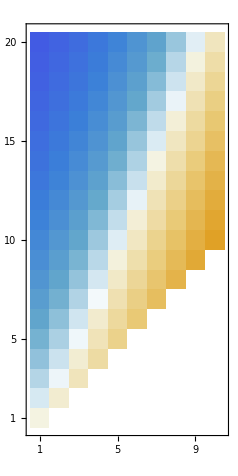

```mathematica
MatrixPlot[Transpose[g], DataReversed->{True,False}]
```